## Analysis of SimTree output

## Basic parameters

```mathematica
demeCount=3;
```

```mathematica
demes={"North","Tropics","South"};
```

```mathematica
clipStartTime=-10;
```

```mathematica
clipEndTime=100;
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/bedfordt/Documents/current-projects/SimTree/source

```mathematica
spatialColors={RGBColor[0.765,0.728,0.274],RGBColor[0.324,0.609,0.708],RGBColor[0.857,0.131,0.132]};
```

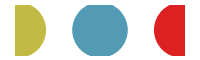

```mathematica
Graphics[{PointSize[0.2],MapIndexed[{#1,Point[{#2[[1]],0}]}&,spatialColors]},AspectRatio->0.3,ImageSize->200]
```

```mathematica
spatialColorRules=MapIndexed[#2[[1]]-1->#1&,spatialColors];
```

```mathematica
trunkColors={GrayLevel[0.3],RGBColor[0.857,0.131,0.132]};
```

```mathematica
trunkColorRules=MapIndexed[#2[[1]]-1->#1&,trunkColors];
```

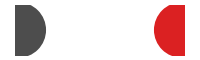

```mathematica
Graphics[{PointSize[0.2],MapIndexed[{#1,Point[{#2[[1]],0}]}&,trunkColors]},AspectRatio->0.3,ImageSize->200]
```

## Loess fit

```mathematica
LoessFit[(x_)?VectorQ,data_,α_:0.75,λ_:1]:=Table[LoessFit[x[[i]],data,α,λ],{i,Length[x]}]
```

```mathematica
LoessFit[(x_)?NumberQ,data_,α_:0.75,λ_:1]:=WLSFit[data,LoessWts[x,data,α],λ,x];
```

```mathematica
WLSFit[data_,wts_,ldegree_:1,x_]:=Fit[Transpose[(wts*#1&)/@Join[{Table[1,{Length[data]}]},Transpose[data]]],Join[{u},Table[v^i,{i,ldegree}]],{u,v}]/.{u->1,v->x}
```

```mathematica
LoessWts[x_,data_,α_]:=Tricube[(x-First[Transpose[data]])/LoessDistance[x,data,α]]
```

```mathematica
Tricube=Compile[{{x,_Real,1}},If[Abs[#]<1,(1-Abs[#]^3)^3,0]&/@x];
```

```mathematica
LoessDistance[x_,data_,α_]:=Module[{A=Max[1,α],X=First[Transpose[data]],q},q=Min[Length[X],Ceiling[α*Length[X]]];A*Sort[Abs[X-x]][[q]]]
```

## Options

```mathematica
SetOptions[Plot,LabelStyle->Directive[Black,FontSize->9,FontFamily->"Helvetica"],Axes->False,Frame->{True,True,False,False},ImageSize->600,PlotRange->{0,All}];
```

```mathematica
SetOptions[ListLinePlot,LabelStyle->Directive[Black,FontSize->9,FontFamily->"Helvetica"],Axes->False,Frame->{True,True,False,False},ImageSize->600,PlotRange->{0,All}];
```

```mathematica
SetOptions[ListPlot,LabelStyle->Directive[Black,FontSize->9,FontFamily->"Helvetica"],Axes->False,Frame->{True,True,False,False},ImageSize->600,PlotRange->{0,All}];
```

```mathematica
SetOptions[ListLogPlot,LabelStyle->Directive[Black,FontSize->9,FontFamily->"Helvetica"],Axes->False,Frame->{True,True,False,False},ImageSize->600,PlotRange->{0,All}];
```

```mathematica
SetOptions[Graphics,LabelStyle->Directive[Black,FontSize->9,FontFamily->"Helvetica"],Axes->False,Frame->False,FrameTicksStyle->Black,ImageSize->600,PlotRange->{0,All}];
```

```mathematica
SetOptions[Histogram,LabelStyle->Directive[Black,FontSize->9,FontFamily->"Helvetica"],Axes->False,Frame->{True,True,False,False},FrameTicksStyle->Black,ImageSize->600,PlotRange->{0,All},ChartStyle->EdgeForm[Thin]];
```

```mathematica
SetOptions[SmoothDensityHistogram,FrameStyle->Directive[Black,FontSize->9,FontFamily->"Helvetica"],Axes->False,Frame->{True,True,False,False},FrameTicksStyle->Black,ImageSize->600,PlotRange->{0,All}];
```

## Assumptions

### R0

5 day recovery

```mathematica
0.2*1.8
```

0.36

### Mutation

Let’s say there are 10 sites that function to move the virus in phenotype space

```mathematica
20*0.005*(1/365)
```

0.000273973

Mutations per day

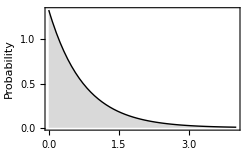

```mathematica
fig=Plot[PDF[ExponentialDistribution[1/0.75],x],{x,0,4},ImageSize->250,Filling->Axis,PlotStyle->Black,FillingStyle->LightGray,FrameLabel->{"Antigenic distance","Probability"}]
```

```mathematica
CDF[ExponentialDistribution[2.],2]
```

0.981684

### Cross-immunity

The antigenic map is on a Log2 scale.

Average distance between clusters is 4.5 units.

Rough cross-immunity between clusters is 0.65 to 0.80.

4.5 units = 0.3 risk of infection

```mathematica
4.5*0.067
```

0.3015

```mathematica
TableForm[N[Table[x*0.067,{x,0,6}]],TableHeadings->{Range[0,6]}]
```

0 | 0.
1 | 0.067
2 | 0.134
3 | 0.201
4 | 0.268
5 | 0.335
6 | 0.402

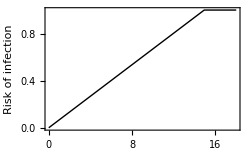

```mathematica
fig=Plot[Clip[x*0.067],{x,0,18},PlotStyle->Black,ImageSize->250,FrameLabel->{"Antigenic distance","Risk of infection"}]
```

## World-wide SIR

```mathematica
data=Import["out.timeseries","Table"];
```

```mathematica
TableForm[data[[1]],TableHeadings->{Range[30]}]
```

1 | date
2 | diversity
3 | totalN
4 | totalS
5 | totalI
6 | totalR
7 | totalCases
8 | northN
9 | northS
10 | northI
11 | northR
12 | northCases
13 | tropicsN
14 | tropicsS
15 | tropicsI
16 | tropicsR
17 | tropicsCases
18 | southN
19 | southS
20 | southI
21 | southR
22 | southCases

```mathematica
data=Drop[data,1];
```

```mathematica
startTime=data[[1,1]]
```

0.0027

```mathematica
endTime=data[[-1,1]]
```

13.7151

```mathematica
popSize=data[[1,3]]
```

2999980

```mathematica
Length[data]
```

5006

### Analysis window

```mathematica
data=Select[data,(#[[1]]>clipStartTime&&#[[1]]<clipEndTime&)];
```

### Yearly incidence

Mean incidence per year

```mathematica
inc=data[[All,{1,7}]];
```

```mathematica
N[(Total[inc[[All,2]]]/endTime)]
```

542923.

```mathematica
meaninc=N[(Total[inc[[All,2]]]/endTime)/popSize]
```

0.180975

Flu incidence is 10% per year and prevalence is 0.14%.

### Pruning

```mathematica
data=data[[1;;-1;;10]];
```

### Prevalence

```mathematica
prev=data[[All,{1,5}]];
```

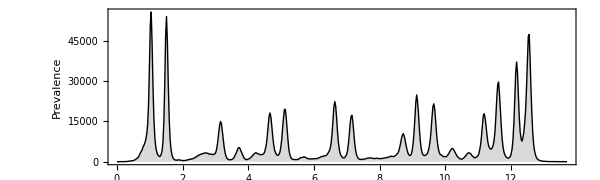

```mathematica
fig=ListLinePlot[prev,AspectRatio->0.3,Filling->Axis,PlotStyle->Black,FillingStyle->LightGray,FrameLabel->{"","Prevalence"},ImagePadding->{{40,10},{15,5}}]
```

```mathematica
Export["prevalence.pdf",fig,"PDF"]
```

prevalence.pdf

### Incidence

```mathematica
inc=data[[All,{1,7}]];
```

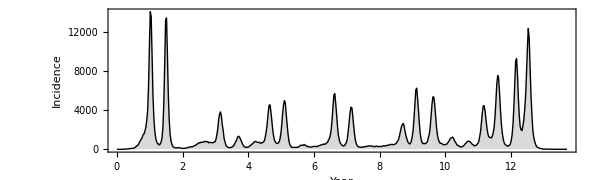

```mathematica
fig=ListLinePlot[inc,AspectRatio->0.3,Filling->Axis,PlotStyle->Black,FillingStyle->LightGray,FrameLabel->{"Year","Incidence"}]
```

```mathematica
Export["incidence.pdf",fig,"PDF"]
```

incidence.pdf

### Diversity

```mathematica
div=data[[All,{1,2}]];
```

```mathematica
meandiv=Mean[div][[2]]
```

3.94669

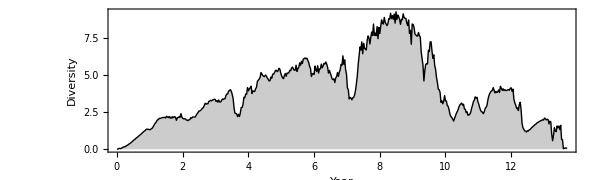

```mathematica
fig=ListLinePlot[div,AspectRatio->0.3,Filling->Axis,PlotStyle->Black,FillingStyle->GrayLevel[0.8],FrameLabel->{"Year","Diversity"}]
```

```mathematica
Export["diversity.pdf",fig,"PDF"]
```

diversity.pdf

## Regional SIR

```mathematica
data=Import["out.timeseries","Table"];
```

```mathematica
TableForm[data[[1]],TableHeadings->{Range[30]}]
```

1 | date
2 | diversity
3 | totalN
4 | totalS
5 | totalI
6 | totalR
7 | totalCases
8 | northN
9 | northS
10 | northI
11 | northR
12 | northCases
13 | tropicsN
14 | tropicsS
15 | tropicsI
16 | tropicsR
17 | tropicsCases
18 | southN
19 | southS
20 | southI
21 | southR
22 | southCases

```mathematica
data=Drop[data,1];
```

```mathematica
startTime=data[[1,1]]
```

0.0027

```mathematica
endTime=data[[-1,1]]
```

13.7151

### Analysis window

```mathematica
data=Select[data,(#[[1]]>clipStartTime&&#[[1]]<clipEndTime&)];
```

### Yearly incidence

```mathematica
incList=Table[data[[All,i]],{i,12,12+(demeCount-1)*5,5}];
```

```mathematica
TableForm[N[Map[Total[#]&,incList]]/(endTime-startTime),TableHeadings->{demes}]
```

North | 191746.
Tropics | 146818.
South | 204466.

```mathematica
{meanIncNorth,meanIncTropics,meanIncSouth}=Map[Total[#]&,incList]/((endTime-startTime)*(popSize/demeCount));
```

```mathematica
TableForm[Round[meanIncSpatial,0.001],TableHeadings->{demes}]
```

North | 0.181
Tropics | 0.144
South | 0.186

### Pruning

```mathematica
data=data[[1;;-1;;10]];
```

### Prevalence

```mathematica
prevList=Table[data[[All,{1,i}]],{i,10,10+(demeCount-1)*5,5}];
```

```mathematica
max=Max[Map[Max,prevList]]
```

53233

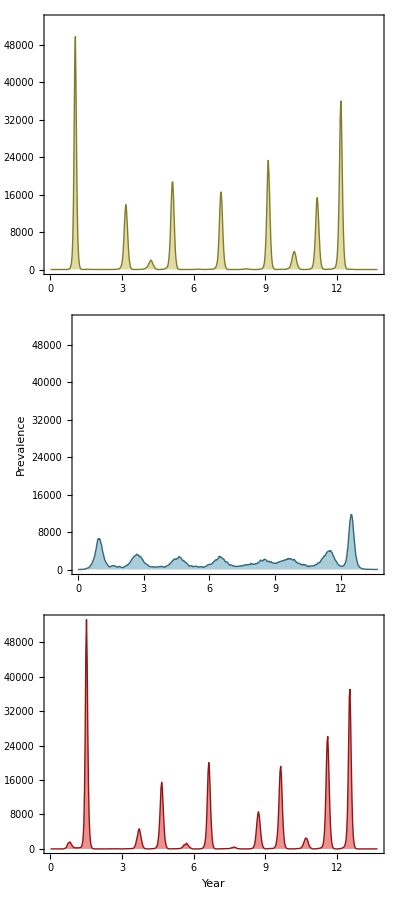

```mathematica
fig=Grid[Table[{ListLinePlot[prevList[[i]],PlotRange->{0,max},AspectRatio->0.2,Filling->Axis,PlotStyle->Darker[spatialColors[[i]]],FillingStyle->Directive[Lighter[spatialColors[[i]],0.5]],FrameLabel->{If[i==demeCount,"Year",""],If[i==2,"Prevalence",""]},ImagePadding->{{50,10},{If[i==demeCount,30,15],5}}]},{i,demeCount}]]
```

```mathematica
Export["prevalenceSpatial.pdf",fig,"PDF"]
```

prevalenceSpatial.pdf

## Tips

```mathematica
tipScale=0.001;
```

```mathematica
tipData=Import["out.tips","CSV"];
```

```mathematica
length=Length[tipData]
```

5949

```mathematica
traitHeader=tipData[[1]];
```

```mathematica
TableForm[traitHeader,TableHeadings->{Range[8]}]
```

1 | name
2 | year
3 | trunk
4 | tip
5 | mark
6 | location
7 | layout
8 | ag1
 | ag2

```mathematica
tipData=Drop[tipData,1];
```

```mathematica
name=1;year=2;trunk=3;tip=4;mark=5;loc=6;layout=7;ag1=8;ag2=9;
```

```mathematica
tipData[[100]]
```

{3de80b2c,0.9616,0,1,0,0,0.,0.,0.}

### Analysis window

```mathematica
tipData=Select[tipData,(#[[year]]>clipStartTime&&#[[year]]<clipEndTime&)];
```

### Rotation

```mathematica
times=tipData[[All,year]];
```

```mathematica
pc=PrincipalComponents[tipData[[All,{ag1,ag2}]]];
```

```mathematica
first=pc[[First[Ordering[times]]]]
```

{3.21206,0.270712}

```mathematica
last=pc[[Last[Ordering[times]]]]
```

{-7.24981,-0.414289}

```mathematica
pc=If[first[[1]]>last[[1]],Map[{-#[[1]],#[[2]]}&,pc],pc];
```

```mathematica
tipData=MapThread[{#1[[name]],#1[[year]],#1[[trunk]],#1[[tip]],#1[[mark]],#1[[loc]],#1[[layout]],#2[[1]],#2[[2]]}&,{tipData,pc}];
```

```mathematica
startingPoint=First[pc]
```

{-3.21206,0.270712}

```mathematica
dist[coord_]:=EuclideanDistance[startingPoint,coord]
```

### Graphics settings

```mathematica
frameWindow=1.0;
```

```mathematica
plotRange={{Floor[Min[tipData[[All,ag1]]],frameWindow],Ceiling[Max[tipData[[All,ag1]]],frameWindow]},{Floor[Min[tipData[[All,ag2]]],frameWindow],Ceiling[Max[tipData[[All,ag2]]],frameWindow]}}
```

{{-5.,10.},{-3.,5.}}

```mathematica
plotRange={{Floor[Quantile[tipData[[All,ag1]],0.01],frameWindow]-1,Ceiling[Quantile[tipData[[All,ag1]],0.99],frameWindow]+1},{Floor[Quantile[tipData[[All,ag2]],0.01],frameWindow]-1,Ceiling[Quantile[tipData[[All,ag2]],0.99],frameWindow]+1}}
```

{{-5.,9.},{-3.,4.}}

```mathematica
aspectRatio=Max[Apply[EuclideanDistance,plotRange[[2]]]/Apply[EuclideanDistance,plotRange[[1]]],0.15]
```

0.5

```mathematica
imageSize=If[aspectRatio>1,600/aspectRatio,600]
```

600

```mathematica
frameTicks=Table[Table[{i,i,{0.01,0}},{i,-100,100,frameWindow}],{2},{2}];
```

### Year vs AG1

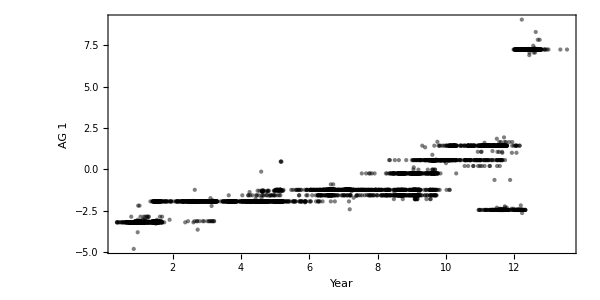

```mathematica
fig=ListPlot[tipData[[All,{year,ag1}]],AspectRatio->0.5,PlotRange->All,PlotStyle->Directive[PointSize[Medium],Black,Opacity[0.5]],FrameLabel->{"Year","AG 1"}]
```

```mathematica
Export["tipsYearAG1.pdf",fig,"PDF"]
```

tipsYearAG1.pdf

### Year vs AG2

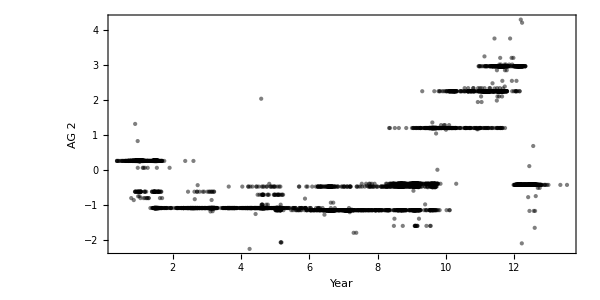

```mathematica
fig=ListPlot[tipData[[All,{year,ag2}]],AspectRatio->0.5,PlotRange->All,PlotStyle->Directive[PointSize[Medium],Black,Opacity[0.5]],FrameLabel->{"Year","AG 2"}]
```

```mathematica
Export["tipsYearAG2.pdf",fig,"PDF"]
```

tipsYearAG2.pdf

### AG1 vs AG2

```mathematica
tallies=Tally[tipData[[All,{ag1,ag2}]]];
```

```mathematica
points=Map[{PointSize[N[tipScale*Sqrt[#[[2]]]]],Point[#[[1]]]}&,tallies];
```

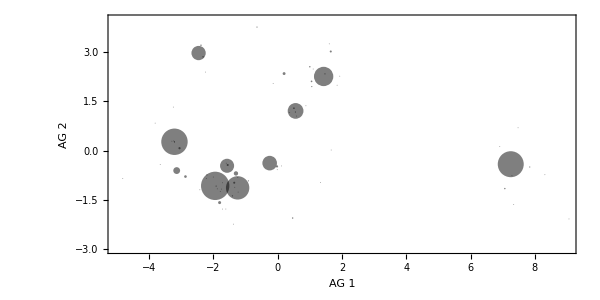

```mathematica
fig=Graphics[{Opacity[0.5],points},AspectRatio->aspectRatio,PlotRange->plotRange,FrameLabel->{"AG 1","AG 2"},Frame->{True,True,False,False}]
```

```mathematica
Export["tipsAG1AG2.pdf",fig,"PDF"]
```

tipsAG1AG2.pdf

### Map

Found average distance between two points of the same strain as 1.6 units

1.6 units is 1.6 * 0.067 = 0.11

```mathematica
spread=0.5;
```

```mathematica
test=Table[RandomVariate[NormalDistribution[0,spread],2],{100}];
```

```mathematica
Mean[Flatten[Table[EuclideanDistance[test[[i]],test[[j]]],{i,Length[test]},{j,i+1,Length[test]}]]]
```

0.894256

```mathematica
jitter=Flatten[Map[Table[#[[1]]+RandomVariate[NormalDistribution[0,spread],2],{Round[#[[2]]]}]&,tallies],1];
```

```mathematica
Length[jitter]
```

5948

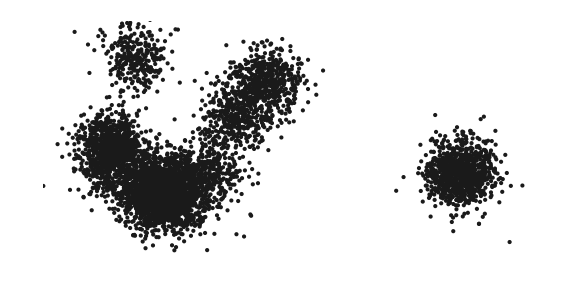

```mathematica
fig=ListPlot[jitter,AspectRatio->aspectRatio,PlotRange->plotRange,PlotStyle->GrayLevel[0.1],GridLines->{Range[-100,100,frameWindow],Range[-100,100,frameWindow]},GridLinesStyle->LightGray,Frame->False,ImageSize->imageSize*0.95]
```

```mathematica
Export["map.pdf",fig,"PDF"]
```

map.pdf

### Clustering

```mathematica
spread=0.5;
```

```mathematica
k=13;
```

```mathematica
step=0.1;
```

```mathematica
clusterColors=Table[ColorData["Rainbow"][i],{i,0,1,1/(k-1)}];
```

```mathematica
clusterColors=RandomSample[clusterColors];
```

```mathematica
length=Length[tipData]
```

5948

```mathematica
jitter=Map[#+RandomVariate[NormalDistribution[0,spread],2]&,tipData[[All,{ag1,ag2}]]];
```

```mathematica
clustered=FindClusters[jitter->Range[length],k,Method->{"Agglomerate","Linkage"->"Average"}];
```

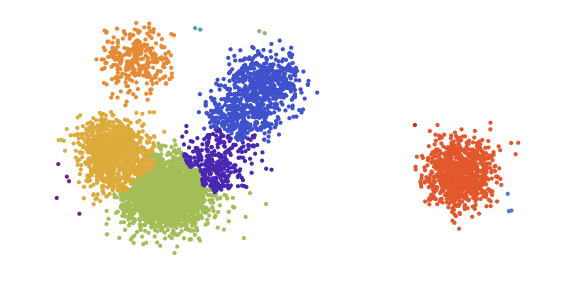

```mathematica
fig=ListPlot[Map[jitter[[#]]&,clustered],PlotStyle->clusterColors,AspectRatio->aspectRatio,PlotRange->plotRange,GridLines->{Range[-100,100,frameWindow],Range[-100,100,frameWindow]},GridLinesStyle->LightGray,Frame->False,ImageSize->imageSize*0.95]
```

```mathematica
Export["mapClusters.pdf",fig,"PDF"]
```

mapClusters.pdf

### Prevalence - clusters

```mathematica
times=tipData[[All,year]];
```

```mathematica
pro=Table[Mean[Map[times[[#]]&,clustered][[i]]],{i,k}];
```

```mathematica
skls=Table[BinCounts[Map[times[[#]]&,clustered][[i]],{startTime,endTime,step}],{i,k}];
```

```mathematica
length=Length[skls[[1]]];
```

```mathematica
ord=Ordering[pro];
```

```mathematica
ordcolorlist=Map[clusterColors[[#]]&,ord];
```

```mathematica
skltable=Table[skls[[i]],{i, ord}];
```

```mathematica
timelist=Map[Mean,Partition[Range[startTime,endTime,step],2,1]];
```

```mathematica
skltable=MapIndexed[{timelist[[#2[[2]]]],#1}&,skltable,{2}];
```

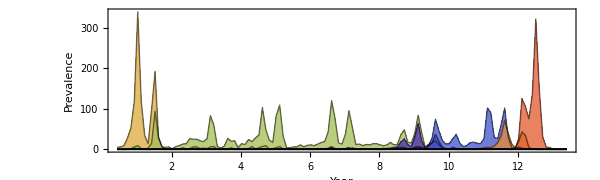

```mathematica
fig=ListLinePlot[skltable,Filling ->Table[i->{Axis,Directive[Opacity[0.75],ordcolorlist[[i]]]},{i,1,k}],PlotStyle->Directive[Opacity[0.5],Black],AspectRatio->0.3,PlotRangePadding->{{0.1,0},{0.05,0}},FrameLabel->{"Year","Prevalence"}]
```

```mathematica
Export["prevalenceClusters.pdf",fig,"PDF"]
```

prevalenceClusters.pdf

### Cluster function

```mathematica
clusterCenters=Map[Mean[jitter[[#]]]&,clustered]
```

{{-3.09057,0.142279},{-1.56097,-1.08767},{-4.71259,-0.871522},{-4.53193,0.7751},{-0.0354393,-0.110056},{1.11294,1.91741},{-2.46101,2.98384},{7.25072,-0.418851},{8.74242,-1.38334},{-2.0246,5.79511},{-0.624144,3.91536},{1.30784,3.81583},{5.90453,1.02479}}

```mathematica
clusterFunction[p_]:=First[Nearest[clusterCenters->Range[k],p]]
```

```mathematica
points=Map[{clusterColors[[clusterFunction[#]]],Point[#]}&,jitter];
```

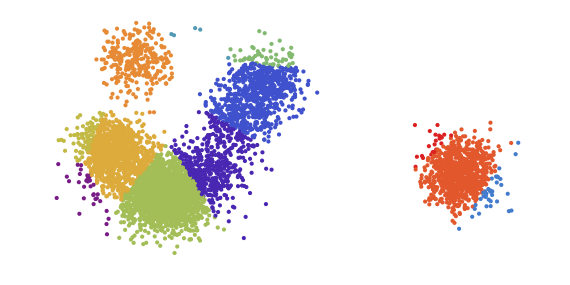

```mathematica
Graphics[points,AspectRatio->aspectRatio,PlotRange->plotRange,GridLines->{Range[-100,100,frameWindow],Range[-100,100,frameWindow]},GridLinesStyle->LightGray,Frame->False,ImageSize->imageSize*0.95]
```

### Distance from origin

```mathematica
list=Map[{#[[1]],dist[#[[{2,3}]]]}&,tipData[[All,{year,ag1,ag2}]]];
```

```mathematica
list[[1]]
```

{0.8548,0.}

AG change per year

```mathematica
meanFluxRate=(Max[list[[All,2]]]-Min[list[[All,2]]])/(endTime-startTime)
```

0.948592

Want 1.2 units per year

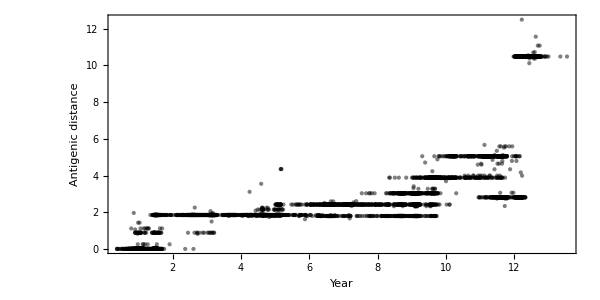

```mathematica
fig=ListPlot[list,AspectRatio->0.5,PlotRange->All,PlotStyle->Directive[PointSize[Medium],Black,Opacity[0.5]],FrameLabel->{"Year","Antigenic distance"}]
```

```mathematica
Export["tipsYearDistance.pdf",fig,"PDF"]
```

tipsYearDistance.pdf

### Loess spline

```mathematica
data=Map[{#[[1]],dist[#[[{2,3}]]]}&,tipData[[All,{year,ag1,ag2}]]];
```

```mathematica
Clear[fit]
```

```mathematica
fit[x_]:=LoessFit[x,data,0.2,1]
```

```mathematica
startTime=Min[data[[All,1]]]
```

0.3671

```mathematica
endTime=Max[data[[All,1]]]
```

13.5425

```mathematica
max=Max[data[[All,2]]]
```

12.4981

```mathematica
loessList=Table[{x,fit[x]},{x,startTime,endTime,0.1}];
```

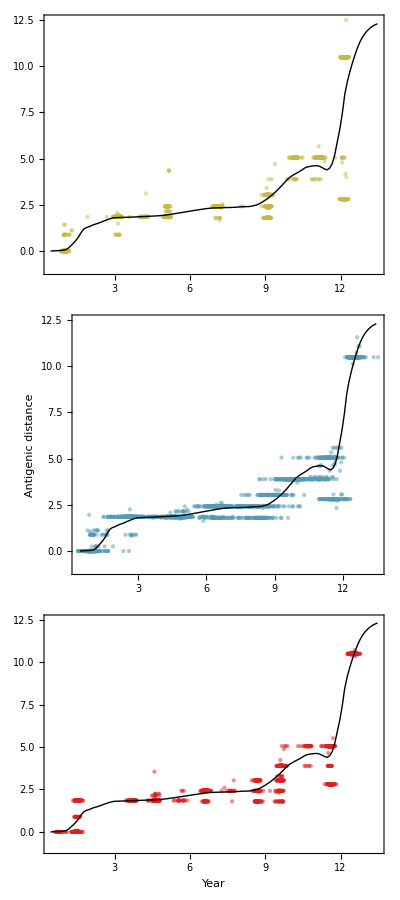

```mathematica
fig=Grid[Table[{Show[ListPlot[Map[{#[[1]],dist[#[[{2,3}]]]}&,Select[tipData,(#[[loc]]==i)&][[All,{year,ag1,ag2}]]],PlotStyle->Directive[i/.spatialColorRules,Opacity[0.5]],PlotRange->{-1,max},ImagePadding->{{30,5},{If[i==2,35,10],5}},AspectRatio->0.5,FrameLabel->{If[i==2,"Year",""],If[i==1,"Antigenic distance",""]},ImageSize->400],ListLinePlot[loessList,PlotStyle->Directive[Black,Thick]]]},{i,0,demeCount-1}]]
```

```mathematica
Export["tipsSplineDistance.pdf",fig,"PDF"]
```

tipsSplineDistance.pdf

```mathematica
distance[list_]:=Module[{nf},
nf=Nearest[loessList[[All,1]]->loessList[[All,2]]];
Map[#[[2]]-First[nf[#[[1]]]]&,list]
]
```

```mathematica
Mean[distance[data]]
```

-0.0228121

```mathematica
standardError[list_]:=StandardDeviation[list]/Sqrt[Length[list]]
```

```mathematica
standardError[distance[data]]
```

0.0133788

```mathematica
spatialDists=Table[With[{dist=distance[Map[{#[[1]],dist[#[[{2,3}]]]}&,Select[tipData,(#[[loc]]==i)&][[All,{year,ag1,ag2}]]]]},{Mean[dist]-standardError[dist],Mean[dist],Mean[dist]+standardError[dist]}],{i,0,demeCount-1}];
```

```mathematica
{meanDistNorth,meanDistTropics,meanDistSouth}=Table[With[{dist=distance[Map[{#[[1]],dist[#[[{2,3}]]]}&,Select[tipData,(#[[loc]]==i)&][[All,{year,ag1,ag2}]]]]},Mean[dist]],{i,0,demeCount-1}];
```

```mathematica
TableForm[Round[spatialDists,0.001],TableHeadings->{demes,{"95% lower","mean","95% upper"}}]
```

| 95% lower | mean | 95% upper
North | 0.031 | 0.064 | 0.098
Tropics | -0.081 | -0.064 | -0.047
South | -0.08 | -0.065 | -0.049

```mathematica
chart=MapIndexed[{GrayLevel[0.3],Line[{{#1[[1]],demeCount-#2[[1]]},{#1[[3]],demeCount-#2[[1]]}}],Line[{{#1[[1]],demeCount-#2[[1]]+0.1},{#1[[1]],demeCount-#2[[1]]-0.1}}],Line[{{#1[[3]],demeCount-#2[[1]]+0.1},{#1[[3]],demeCount-#2[[1]]-0.1}}],PointSize[0.03],spatialColors[[#2[[1]]]],Point[{#1[[2]],demeCount-#2[[1]]}]}&,spatialDists];
```

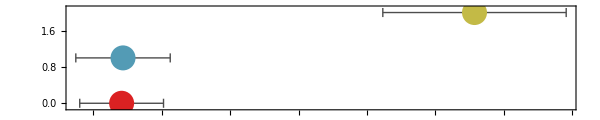

```mathematica
fig=Graphics[chart,AspectRatio->0.2,PlotRange->All,Frame->{True,False,True,False},PlotRangePadding->{{0,0},{0.5,0.5}},FrameLabel->{"Distance to AG spline"}]
```

```mathematica
Export["distAGSpatial.pdf",fig,"PDF"]
```

distAGSpatial.pdf

## Trees

First node is child, second is parent

```mathematica
branchScale=0.001;tipScale=0.002;clip=0.005;
```

```mathematica
getThickness[count_]:=Thickness[Clip[branchScale*N[Sqrt[count]],{0,clip}]]
```

```mathematica
getPointSize[count_]:=PointSize[N[tipScale*Sqrt[count]]];
```

```mathematica
name=1;year=2;trunk=3;tip=4;mark=5;loc=6;layout=7;ag1=8;ag2=9;
```

```mathematica
branchData=ToExpression[Import["out.branches","Table"]];
```

```mathematica
branchData[[1]]
```

{{3040c5,0.1151,0,0,1,1,259.779,0.,0.},{2b9cd6b6,0.,0,0,1,0,259.779,0.,0.},5948}

```mathematica
branchData[[1,{1,2},{year,layout}]]
```

{{0.1151,259.779},{0.,259.779}}

```mathematica
Length[branchData]
```

53632

### Analysis window

```mathematica
branchData=Select[branchData,(#[[1,year]]>clipStartTime&&#[[1,year]]<clipEndTime&&#[[2,year]]>clipStartTime&&#[[2,year]]<clipEndTime&)];
```

### Rotation

```mathematica
length=Length[branchData[[All,1,year]]];
```

```mathematica
times=Join[branchData[[All,1,year]],branchData[[All,2,year]]];
```

```mathematica
pc=PrincipalComponents[Join[branchData[[All,1,{ag1,ag2}]],branchData[[All,2,{ag1,ag2}]]]];
```

```mathematica
first=pc[[First[Ordering[times]]]];
```

```mathematica
last=pc[[Last[Ordering[times]]]];
```

```mathematica
pc=If[first[[1]]>last[[1]],Map[{-#[[1]],#[[2]]}&,pc],pc];
```

```mathematica
pc=Transpose[{pc[[1;;length]],pc[[length+1;;-1]]}];
```

```mathematica
branchData=MapThread[{{#1[[1,name]],#1[[1,year]],#1[[1,trunk]],#1[[1,tip]],#1[[1,mark]],#1[[1,loc]],#1[[1,layout]],#2[[1,1]],#2[[1,2]]},{#1[[2,name]],#1[[2,year]],#1[[2,trunk]],#1[[2,tip]],#1[[2,mark]],#1[[2,loc]],#1[[2,layout]],#2[[2,1]],#2[[2,2]]},#1[[3]]}&,{branchData,pc}];
```

```mathematica
startingPoint=If[first[[1]]>last[[1]],last,first];
```

```mathematica
dist[coord_]:=EuclideanDistance[startingPoint,coord]
```

### Reduction

```mathematica
slimBranches=Select[branchData,(#[[1,mark]]==1&&#[[2,mark]]==1&)];
```

```mathematica
Length[slimBranches]
```

8050

### Time vs Layout

```mathematica
branchLines=Map[{getThickness[#[[3]]],#[[1,trunk]]/.trunkColorRules,Line[{#[[1,{year,layout}]],{#[[2,year]],#[[1,layout]]},#[[2,{year,layout}]]}]}&,slimBranches];
```

```mathematica
branchLines={CapForm["Round"],branchLines};
```

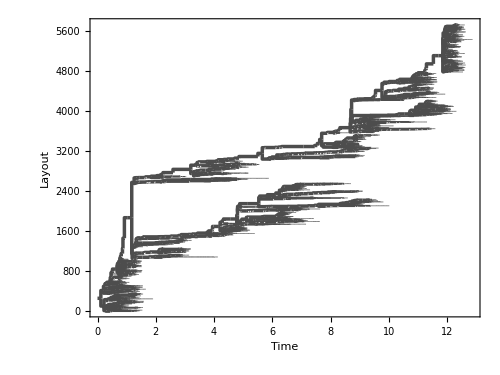

```mathematica
fig=Graphics[branchLines,AspectRatio->0.75,ImageSize->500,PlotRange->All,FrameLabel->{"Time","Layout"},Frame->{True,False,False,False}]
```

```mathematica
Export["tree.pdf",fig,"PDF"]
```

tree.pdf

### Time vs Layout - clusters

```mathematica
branchLines=Map[{getThickness[#[[3]]],clusterColors[[clusterFunction[#[[1,{ag1,ag2}]]]]],Line[{#[[1,{year,layout}]],{#[[2,year]],#[[1,layout]]},#[[2,{year,layout}]]}]}&,slimBranches];
```

```mathematica
branchLines={CapForm["Round"],branchLines};
```

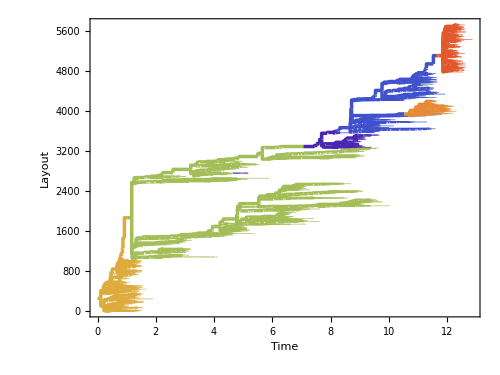

```mathematica
fig=Graphics[branchLines,AspectRatio->0.75,PlotRange->All,ImageSize->500,FrameLabel->{"Time","Layout"},Frame->{True,False,False,False}]
```

```mathematica
Export["treeClusters.pdf",fig,"PDF"]
```

treeClusters.pdf

### Time vs Layout with location

```mathematica
branchLines=Map[{getThickness[#[[3]]],#[[1,loc]]/.spatialColorRules,Line[{#[[1,{year,layout}]],{#[[2,year]],#[[1,layout]]},#[[2,{year,layout}]]}]}&,slimBranches];
```

```mathematica
branchLines={CapForm["Round"],branchLines};
```

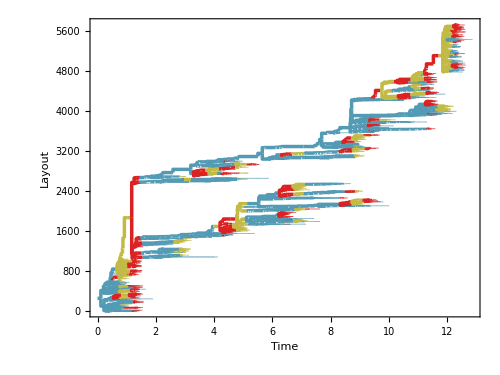

```mathematica
fig=Graphics[branchLines,AspectRatio->0.75,PlotRange->All,ImageSize->500,FrameLabel->{"Time","Layout"},Frame->{True,False,False,False}]
```

```mathematica
Export["treeSpatial.pdf",fig,"PDF"]
```

treeSpatial.pdf

### AG1 vs AG2

```mathematica
mutBranches=Select[branchData,(EuclideanDistance[#[[1,{ag1,ag2}]],#[[2,{ag1,ag2}]]]>0.0000001&)];
```

```mathematica
Length[mutBranches]
```

78

```mathematica
branchLines=Map[{getThickness[#[[3]]],#[[1,trunk]]/.trunkColorRules,Line[{#[[1,{ag1,ag2}]],Mean[{#[[1,{ag1,ag2}]],#[[2,{ag1,ag2}]]}]}],#[[2,trunk]]/.trunkColorRules,Line[{Mean[{#[[1,{ag1,ag2}]],#[[2,{ag1,ag2}]]}],#[[2,{ag1,ag2}]]}]}&,mutBranches];
```

```mathematica
branchLines={CapForm["Round"],branchLines};
```

```mathematica
tipBranches=Select[branchData,(#[[1,tip]]==1&)];
```

```mathematica
tallies=Tally[tipBranches[[All,1,{ag1,ag2}]]];
```

```mathematica
tipPoints=Map[{getPointSize[#[[2]]],0/.trunkColorRules,Point[#[[1]]]}&,tallies];
```

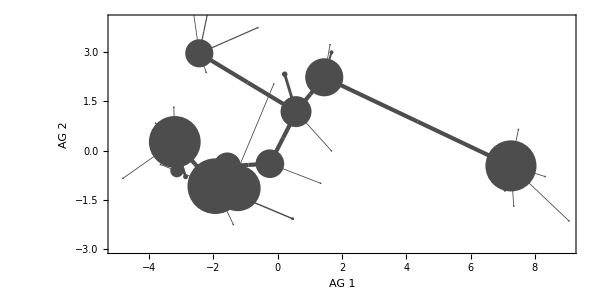

```mathematica
fig=Graphics[{branchLines,tipPoints},AspectRatio->aspectRatio,PlotRange->plotRange,ImageSize->imageSize,FrameLabel->{"AG 1","AG 2"},Frame->{True,True,False,False}]
```

```mathematica
Export["treeAG1AG2.pdf",fig,"PDF"]
```

treeAG1AG2.pdf

### AG1 vs AG2 with clusters

```mathematica
mutBranches=Select[branchData,(EuclideanDistance[#[[1,{ag1,ag2}]],#[[2,{ag1,ag2}]]]>0.0000001&)];
```

```mathematica
branchLines=Map[{getThickness[#[[3]]],clusterColors[[clusterFunction[#[[1,{ag1,ag2}]]]]],Line[{#[[1,{ag1,ag2}]],Mean[{#[[1,{ag1,ag2}]],#[[2,{ag1,ag2}]]}]}],clusterColors[[clusterFunction[#[[2,{ag1,ag2}]]]]],Line[{Mean[{#[[1,{ag1,ag2}]],#[[2,{ag1,ag2}]]}],#[[2,{ag1,ag2}]]}]}&,mutBranches];
```

```mathematica
branchLines={CapForm["Round"],branchLines};
```

```mathematica
tipBranches=Select[branchData,(#[[1,tip]]==1&)];
```

```mathematica
tallies=Tally[tipBranches[[All,1,{ag1,ag2}]]];
```

```mathematica
tipPoints=Map[{getPointSize[#[[2]]],clusterColors[[clusterFunction[#[[1]]]]],Point[#[[1]]]}&,tallies];
```

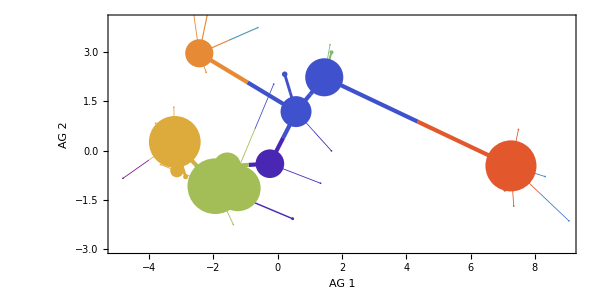

```mathematica
fig=Graphics[{branchLines,tipPoints},AspectRatio->aspectRatio,PlotRange->plotRange,ImageSize->imageSize,FrameLabel->{"AG 1","AG 2"},Frame->{True,True,False,False}]
```

```mathematica
Export["treeAG1AG2Clusters.pdf",fig,"PDF"]
```

treeAG1AG2Clusters.pdf

## Mutation statistics

```mathematica
trunkBranches=Select[branchData,(#[[1,trunk]]==1&&#[[1,year]]<endTime-1&)];
```

```mathematica
sideBranches=Select[branchData,(#[[1,trunk]]==0&&#[[1,year]]<endTime-1&)];
```

### Baseline

```mathematica
baselineMutationRate=0.00014*365;
```

```mathematica
baselineMutationSize=0.75;
```

```mathematica
baselineFluxRate=baselineMutationRate*baselineMutationSize;
```

### Mutation rate

```mathematica
trunkOpportunity=Total[Map[Abs[#[[1,year]]-#[[2,year]]]&,trunkBranches]];
```

```mathematica
sideBranchOpportunity=Total[Map[Abs[#[[1,year]]-#[[2,year]]]&,sideBranches]];
```

```mathematica
trunkCount=Total[Map[If[EuclideanDistance[#[[1,{ag1,ag2}]],#[[2,{ag1,ag2}]]]>0.0000001,1,0]&,trunkBranches]];
```

```mathematica
sideBranchCount=Total[Map[If[EuclideanDistance[#[[1,{ag1,ag2}]],#[[2,{ag1,ag2}]]]>0.0000001,1,0]&,sideBranches]];
```

```mathematica
trunkMutationRate=trunkCount/trunkOpportunity
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

Indeterminate

```mathematica
sideBranchMutationRate=sideBranchCount/sideBranchOpportunity
```

0.0546631

### Antigenic flux

```mathematica
trunkOpportunity=Total[Map[Abs[#[[1,year]]-#[[2,year]]]&,trunkBranches]];
```

```mathematica
sideBranchOpportunity=Total[Map[Abs[#[[1,year]]-#[[2,year]]]&,sideBranches]];
```

```mathematica
trunkDistance=Total[Map[EuclideanDistance[#[[1,{ag1,ag2}]],#[[2,{ag1,ag2}]]]&,trunkBranches]];
```

```mathematica
sideBranchDistance=Total[Map[EuclideanDistance[#[[1,{ag1,ag2}]],#[[2,{ag1,ag2}]]]&,sideBranches]];
```

```mathematica
trunkFluxRate=trunkDistance/trunkOpportunity
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

Indeterminate

```mathematica
sideBranchFluxRate=sideBranchDistance/sideBranchOpportunity
```

0.0477336

### Mutation size

```mathematica
trunkMutations=Select[Map[EuclideanDistance[#[[1,{ag1,ag2}]],#[[2,{ag1,ag2}]]]&,trunkBranches],#>0.0000001&];
```

```mathematica
sideBranchMutations=Select[Map[EuclideanDistance[#[[1,{ag1,ag2}]],#[[2,{ag1,ag2}]]]&,sideBranches],#>0.0000001&];
```

```mathematica
trunkMutationSize=Mean[trunkMutations]
```

Mean[{}]

```mathematica
sideBranchMutationSize=Mean[sideBranchMutations]
```

0.873232

```mathematica
TableForm[Round[{{baselineMutationRate,baselineMutationSize,baselineFluxRate},{sideBranchMutationRate,sideBranchMutationSize,sideBranchFluxRate},{trunkMutationRate,trunkMutationSize,trunkFluxRate}},0.001],TableHeadings->{{"Mutational baseline","Side branches","Trunk branches"},{"Mutation rate","Mutation size","Antigenic flux"}}]
```

| Mutation rate | Mutation size | Antigenic flux
Mutational baseline | 0.051 | 0.75 | 0.038
Side branches | 0.055 | 0.873 | 0.048
Trunk branches | Indeterminate | Round[Mean[{}],0.001] | Indeterminate

### Mutation spectrum

Forward movement

```mathematica
comparisonHistogram[list_,col_]:=Histogram[list,{0.25},"PDF",PlotRange->{{-4,4},{0,1}},ChartStyle->Directive[EdgeForm[Thin],col],ImageSize->300,Axes->False,Frame->{True,True,False,False}];
```

```mathematica
comparisonDensityHistogram[list_,col_]:=SmoothDensityHistogram[list,0.5,ColorFunction->(Blend[{White,col},#]&),Mesh->20,PlotRange->{{-4,4},{-3.5,3.5}},AspectRatio->Automatic,ImageSize->300,Frame->{True,True,False,False},Axes->True,AxesStyle->Dashed]
```

```mathematica
sideBranchMutations2D=Select[Map[#[[1,{ag1,ag2}]]-#[[2,{ag1,ag2}]]&,sideBranches],(Round[#[[1]],0.0000001]≠0&&Round[#[[2]],0.0000001]≠0&)];
```

```mathematica
trunkMutations2D=Select[Map[#[[1,{ag1,ag2}]]-#[[2,{ag1,ag2}]]&,trunkBranches],(Round[#[[1]],0.0000001]≠0&&Round[#[[2]],0.0000001]≠0&)];
```

SmoothDensityHistogram::ldata: {} is not a valid dataset or list of datasets.

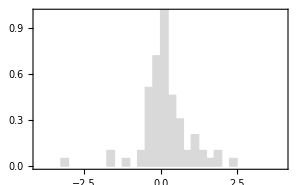
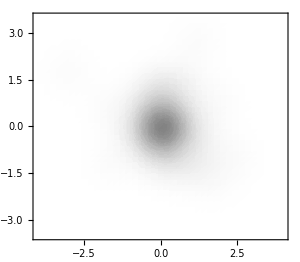
-Graphics- | -Graphics-
-Graphics- | SmoothDensityHistogram[{},0.5,ColorFunction→(Blend[{White,RGBColor[1,0,0]},#1]&),Mesh→20,PlotRange→{{-4,4},{-3.5,3.5}},AspectRatio→Automatic,ImageSize→300,Frame→{True,True,False,False},Axes→True,AxesStyle→Dashing[{Small,Small}]]

```mathematica
fig=Grid[{{comparisonHistogram[sideBranchMutations2D[[All,1]],LightGray],comparisonHistogram[trunkMutations2D[[All,1]],LightRed]},{comparisonDensityHistogram[sideBranchMutations2D,Gray],comparisonDensityHistogram[trunkMutations2D,Red]}},Spacings->{1,1}]
```

```mathematica
Export["mutationSpectrum.pdf",fig,"PDF"]
```

$Aborted

### Hazard function

```mathematica
mutTimes=Sort[Flatten[Map[If[EuclideanDistance[#[[1,{ag1,ag2}]],#[[2,{ag1,ag2}]]]>0.0000001,#[[1,year]],{}]&,trunkBranches]]]
```

{1.1589,1.9534,2.6548,3.5233,3.7041,4.2822,7.2877,8.4082,8.4904,13.2438,14.5425,16.0329,17.4603,19.9151,24.2849,25.1342,27.1233,29.1836,33.1589,35.0301,35.6356,37.0219,38.8466}

```mathematica
waitTimes=Differences[mutTimes]
```

{0.7945,0.7014,0.8685,0.1808,0.5781,3.0055,1.1205,0.0822,4.7534,1.2987,1.4904,1.4274,2.4548,4.3698,0.8493,1.9891,2.0603,3.9753,1.8712,0.6055,1.3863,1.8247}

```mathematica
Mean[waitTimes]
```

1.71308

```mathematica
waitTimeObs=SmoothKernelDistribution[waitTimes,0.3]
```

DataDistribution[«SmoothKernel»,{22}]

```mathematica
waitTimeObs=HistogramDistribution[waitTimes,{0.25}]
```

DataDistribution[«Histogram»,{22}]

```mathematica
waitTimeExp=ExponentialDistribution[1/Mean[waitTimes]]
```

ExponentialDistribution[0.583745]

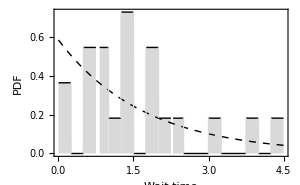

```mathematica
fig1=Plot[{PDF[waitTimeObs,x],PDF[waitTimeExp,x]},{x,0,4.5},Filling->{1->Axis},ImageSize->300,PlotStyle->{Black,Directive[Dashed,Black]},FillingStyle->LightGray,FrameLabel->{"Wait time","PDF"}]
```

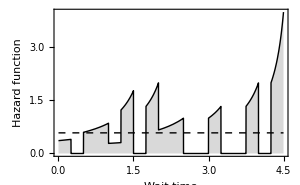

```mathematica
fig2=Plot[{HazardFunction[waitTimeObs,x],HazardFunction[waitTimeExp,x]},{x,0,4.5},Filling->{1->Axis},ImageSize->300,PlotStyle->{Black,Directive[Dashed,Black]},FillingStyle->LightGray,FrameLabel->{"Wait time","Hazard function"}]
```

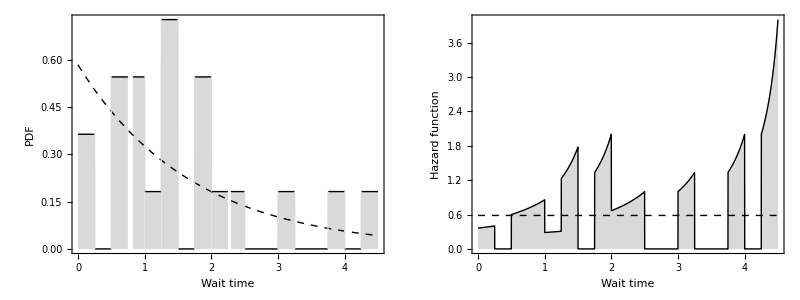

```mathematica
fig=Grid[{{fig1,fig2}}]
```

```mathematica
Export["mutationTiming.pdf",fig,"PDF"]
```

mutationTiming.pdf

```mathematica
TableForm[Round[{{Mean[waitTimeExp],Variance[waitTimeExp]},{Mean[waitTimeObs],Variance[waitTimeObs]}},0.001],TableHeadings->{{"Expected","Observed"},{"Mean","Variance"}}]
```

| Mean | Variance
Expected | 1.713 | 2.935
Observed | 1.716 | 1.639

## Migration statistics

```mathematica
trunkBranches=Select[branchData,(#[[1,trunk]]==1&&#[[1,year]]<endTime-1&)];
```

```mathematica
sideBranches=Select[branchData,(#[[1,trunk]]==0&&#[[1,year]]<endTime-1&)];
```

### Proportion of each deme in trunk

```mathematica
trunkLengths=Table[Total[Map[Abs[#[[1,year]]-#[[2,year]]]&,Select[trunkBranches,(#[[1,loc]]==i&&#[[2,loc]]==i&)]]],{i,0,demeCount-1}];
```

```mathematica
trunkProportions=trunkLengths/Total[trunkLengths];
```

```mathematica
{trunkProNorth,trunkProTropics,trunkProSouth}=trunkLengths/Total[trunkLengths];
```

```mathematica
TableForm[Round[trunkProportions,0.001],TableHeadings->{demes}]
```

North | 0.057
Tropics | 0.898
South | 0.045

### Migration rate

```mathematica
trunkOpportunity=Total[Map[Abs[#[[1,year]]-#[[2,year]]]&,trunkBranches]];
```

```mathematica
sideBranchOpportunity=Total[Map[Abs[#[[1,year]]-#[[2,year]]]&,sideBranches]];
```

```mathematica
trunkCount=Total[Map[If[#[[1,loc]]≠#[[2,loc]],1,0]&,trunkBranches]];
```

```mathematica
sideBranchCount=Total[Map[If[#[[1,loc]]≠#[[2,loc]],1,0]&,sideBranches]];
```

```mathematica
trunkMigRate=trunkCount/trunkOpportunity
```

0.647122

```mathematica
sideBranchMigRate=sideBranchCount/sideBranchOpportunity
```

0.807653

### Migration spectrum

```mathematica
trunkCounts=Table[Total[Map[If[#[[1,loc]]==j&&#[[2,loc]]==i,1,0]&,trunkBranches]],{i,0,demeCount-1},{j,0,demeCount-1}];
```

```mathematica
trunkOpportunies=Table[Total[Map[If[#[[1,loc]]==i&&#[[2,loc]]==i,Abs[#[[1,year]]-#[[2,year]]],0]&,trunkBranches]],{i,0,demeCount-1},{j,0,demeCount-1}];
```

```mathematica
trunkRates=(trunkCounts/trunkOpportunies)*(1-DiagonalMatrix[Table[1,{demeCount}]]);
```

```mathematica
TableForm[Round[trunkRates,0.001]/.(0.->""),TableHeadings->{demes,demes}]
```

| North | Tropics | South
North |  | 2.313 | 2.313
Tropics | 0.177 |  | 0.118
South | 1.766 | 2.943 |

```mathematica
sideBranchCounts=Table[Total[Map[If[#[[1,loc]]==j&&#[[2,loc]]==i,1,0]&,sideBranches]],{i,0,demeCount-1},{j,0,demeCount-1}];
```

```mathematica
sideBranchOpportunies=Table[Total[Map[If[#[[1,loc]]==i&&#[[2,loc]]==i,Abs[#[[1,year]]-#[[2,year]]],0]&,sideBranches]],{i,0,demeCount-1},{j,0,demeCount-1}];
```

```mathematica
sideBranchRates=(sideBranchCounts/sideBranchOpportunies)*(1-DiagonalMatrix[Table[1,{demeCount}]]);
```

```mathematica
TableForm[Round[sideBranchRates,0.001]/.(0.->""),TableHeadings->{demes,demes}]
```

| North | Tropics | South
North |  | 0.244 | 0.962
Tropics | 0.336 |  | 0.276
South | 0.768 | 0.357 |

### Seasonal migration spectrum

```mathematica
seasonalMigRate[branches_,start_,stop_]:=Module[{goodBranches,opportunities,counts},
goodBranches=Select[branches,(FractionalPart[#[[1,year]]]<stop&&FractionalPart[#[[2,year]]]≥start)&];
opportunities=Table[Total[Map[If[#[[1,loc]]==i&&#[[2,loc]]==i,Abs[#[[1,year]]-#[[2,year]]],0]&,goodBranches]],{i,0,demeCount-1},{j,0,demeCount-1}];
counts=Table[Total[Map[If[#[[1,loc]]==j&&#[[2,loc]]==i,1,0]&,goodBranches]],{i,0,demeCount-1},{j,0,demeCount-1}];
(counts/opportunities)*(1-DiagonalMatrix[Table[1,{demeCount}]])
]
```

```mathematica
Grid[Table[{TableForm[Round[seasonalMigRate[branchData,i,i+0.25],0.001],TableHeadings->{demes,demes}]},{i,0,0.75,0.25}],Spacings->{2,2}]
```

| North | Tropics | South
North | 0. | 0.485 | 1.347
Tropics | 0.069 | 0. | 0.234
South | 0.891 | 0.891 | 0.
 | North | Tropics | South
North | 0. | 0.303 | 2.221
Tropics | 0.093 | 0. | 0.609
South | 0.098 | 0.122 | 0.
 | North | Tropics | South
North | 0. | 0.084 | 0.084
Tropics | 0.313 | 0. | 0.041
South | 1.049 | 0.809 | 0.
 | North | Tropics | South
North | 0. | 0.061 | 0.02
Tropics | 0.955 | 0. | 0.
South | 20.583 | 0.686 | 0.

### Mutation rate - spatial

```mathematica
rates=Table[
branches=Select[branchData,(#[[1,loc]]==i&&#[[2,loc]]==i&)];
opportunity=Total[Map[Abs[#[[1,year]]-#[[2,year]]]&,branches]];
count=Total[Map[If[EuclideanDistance[#[[1,{ag1,ag2}]],#[[2,{ag1,ag2}]]]>0,1,0]&,branches]];
rate=count/opportunity,
{i,0,demeCount-1}];
```

```mathematica
TableForm[Round[rates,0.001],TableHeadings->{demes}]
```

North | 0.13
Tropics | 0.122
South | 0.042

### Antigenic flux - spatial

```mathematica
rates=Table[
branches=Select[branchData,(#[[1,loc]]==i&&#[[2,loc]]==i&)];
opportunity=Total[Map[Abs[#[[1,year]]-#[[2,year]]]&,branches]];
antigenicDistance=Total[Map[EuclideanDistance[#[[1,{ag1,ag2}]],#[[2,{ag1,ag2}]]]&,branches]];
rate=antigenicDistance/opportunity,
{i,0,demeCount-1}];
```

```mathematica
{fluxRateNorth,fluxRateTropics,fluxRateSouth}=Table[
branches=Select[branchData,(#[[1,loc]]==i&&#[[2,loc]]==i&)];
opportunity=Total[Map[Abs[#[[1,year]]-#[[2,year]]]&,branches]];
antigenicDistance=Total[Map[EuclideanDistance[#[[1,{ag1,ag2}]],#[[2,{ag1,ag2}]]]&,branches]];
rate=antigenicDistance/opportunity,
{i,0,demeCount-1}];
```

```mathematica
TableForm[Round[rates,0.001],TableHeadings->{demes}]
```

North | 0.251
Tropics | 0.19
South | 0.047

### Antigenic flux - spatial - absolute

```mathematica
rates=Table[
branches=Select[branchData,(#[[1,loc]]==i&&#[[2,loc]]==i&)];
antigenicDistance=Total[Map[EuclideanDistance[#[[1,{ag1,ag2}]],#[[2,{ag1,ag2}]]]&,branches]];
antigenicDistance,
{i,0,demeCount-1}];
```

```mathematica
TableForm[Round[rates,0.001],TableHeadings->{demes}]
```

North | 21.237
Tropics | 54.699
South | 4.512

## Summary output

```mathematica
statList={meaninc,meandiv,meanIncNorth,meanIncTropics,meanIncSouth,meanFluxRate,meanDistNorth,meanDistTropics,meanDistSouth,sideBranchMutationRate,sideBranchMutationSize,sideBranchFluxRate,trunkMutationRate,trunkMutationSize,trunkFluxRate,trunkProNorth,trunkProTropics,trunkProSouth,sideBranchMigRate,trunkMigRate,fluxRateNorth,fluxRateTropics,fluxRateSouth};
```

```mathematica
statList=Join[statList,{sideBranchMutations2D[[All,1]]},{sideBranchMutations2D[[All,2]]},{trunkMutations2D[[All,1]]},{trunkMutations2D[[All,2]]},{waitTimes}];
```

```mathematica
Export["out.statistics",statList,"Table"]
```

out.statistics

## Animation

```mathematica
tLines[time_]:=Module[{data,branchLines},
data=Select[branchData,(#[[1,year]]<time&&#[[2,year]]<time&)];branchLines=Map[{getThickness[#[[3]]],clusterColors[[clusterFunction[#[[1,{ag1,ag2}]]]]],Line[{#[[1,{ag1,ag2}]],#[[2,{ag1,ag2}]]}]}&,data];
{CapForm["Round"],branchLines}]
```

```mathematica
tPoints[time_]:=Module[{data,tallies,tipPoints},
data=Select[branchData,(#[[1,year]]<time&&#[[2,year]]<time&)];
tallies=Tally[Join[data[[All,1,{ag1,ag2}]],data[[All,2,{ag1,ag2}]]]];
tipPoints=Map[{getPointSize[#[[2]]],clusterColors[[clusterFunction[#[[1]]]]],Point[#[[1]]]}&,tallies];
tipPoints
]
```

```mathematica
frame[time_]:=Graphics[{tLines[time],tPoints[time]},AspectRatio->aspectRatio,PlotRange->plotRange,ImageSize->imageSize,FrameLabel->{"AG1","AG2"},Frame->{True,True,False,False},ImageSize->1000]
```

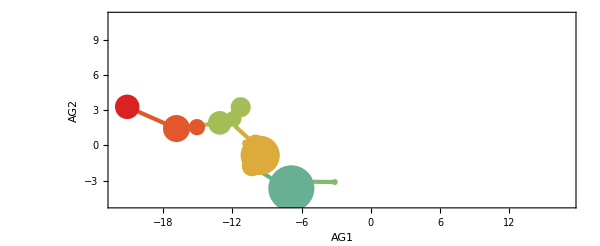

```mathematica
frame[15]
```

Do[f = frame[i]; Export["frames/" <> ToString[IntegerPart[i*10]] <> ".jpg", f, "JPG"];, {i, startTime, endTime, 0.1}]